```mathematica
Simplify@D[4ϵ((σ/r)^12-(σ/r)^6),r]
```

(24 ϵ σ^6 (r^6-2 σ^6))/r^13

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

-Graphics3D-

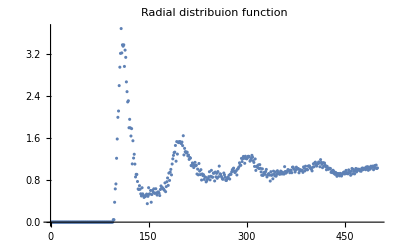

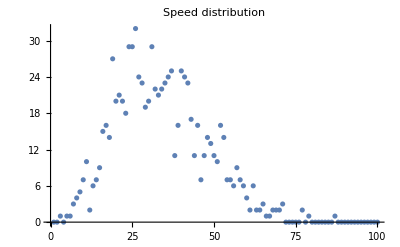

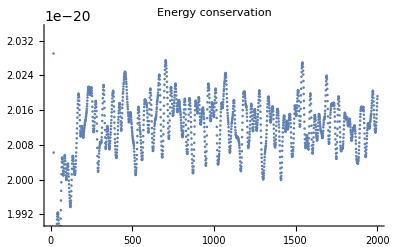

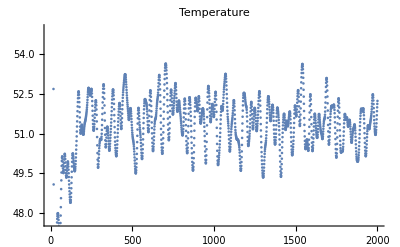

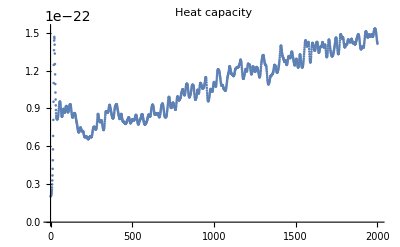

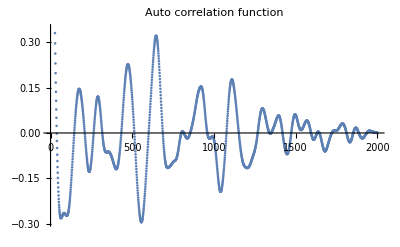

```mathematica
Needs["ErrorBarPlots`"];

scaleFactor=10^0;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/positions.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"},PlotLabel->"Positions"]

velocities= ReadList["~/phd-stuff/courses/astrid_sim/velocities.txt",Number,RecordLists->False];
sortvelocities=Sort[Flatten@velocities];

rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->False];
ListPlot[rdf,PlotLabel->"Radial distribuion function"]

veldist = ReadList["~/phd-stuff/courses/astrid_sim/speeddist.txt",Number,RecordLists->False];
ListPlot[veldist,PlotLabel->"Speed distribution"]

kinetic= ReadList["~/phd-stuff/courses/astrid_sim/kinetic.txt",Number,RecordLists->False];
ListPlot[kinetic,PlotLabel->"Kinnetic energy"];

potential = ReadList["~/phd-stuff/courses/astrid_sim/potential.txt",Number,RecordLists->False];
ListPlot[potential,PlotLabel->"Potential energy"];

energycons = kinetic - potential;
ListPlot[energycons,PlotLabel->"Energy conservation"]

temperature = ReadList["~/phd-stuff/courses/astrid_sim/temperature.txt",Number,RecordLists->False];
ListPlot[temperature,PlotLabel->"Temperature"]

heatcap = ReadList["~/phd-stuff/courses/astrid_sim/heatcapacity.txt",Number,RecordLists->False];
ListPlot[heatcap,PlotLabel->"Heat capacity"]

(*heatcap = ReadList["~/phd-stuff/courses/astrid_sim/mcheatcap.txt",Number,RecordLists->False];
ListPlot[heatcap,PlotLabel->"MC Heat capacity"]*)

correlation = ReadList["~/phd-stuff/courses/astrid_sim/correlation.txt",Number,RecordLists->False];
ListPlot[correlation,PlotLabel->"Auto correlation function"]
```

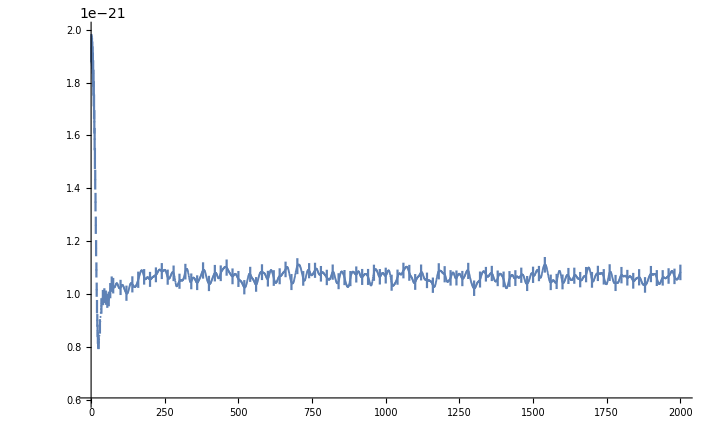

```mathematica
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True];
a=Table[{{1i,kinetic[[1i]]},ErrorBar[error1[[1i]][[1]]]},{i,1,25}];
b=Table[{{5i,kinetic[[5i]]},ErrorBar[error1[[5i]][[1]]]},{i,5,15}];
c=Table[{{20i,kinetic[[20i]]},ErrorBar[error1[[20i]][[1]]]},{i,5,100}];
d=Join[a,b,c];
e=ListPlot[kinetic,PlotRange->{{0,2000},{6*^-22,2*^-21}},PlotStyle->PointSize[0.002]];
f=ErrorListPlot[d,PlotRange->{{0,2000},{6*^-22,2*^-21}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

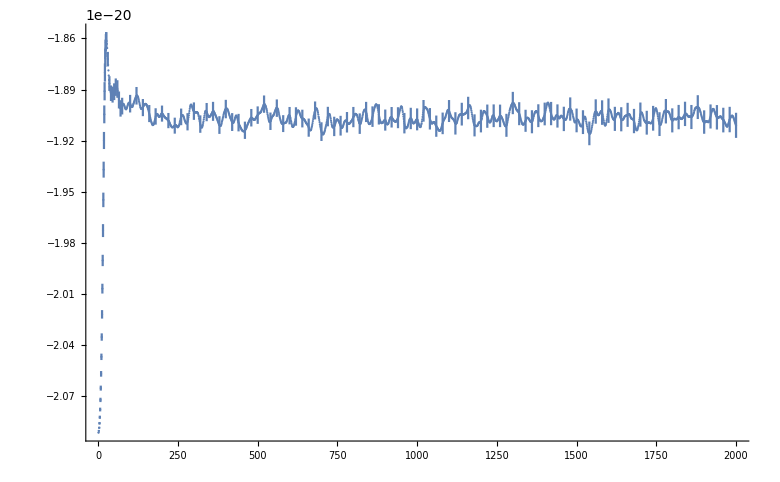

```mathematica
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True];
a=Table[{{1i,potential[[1i]]},ErrorBar[error1[[1i]][[3]]]},{i,1,25}];
b=Table[{{5i,potential[[5i]]},ErrorBar[error1[[5i]][[3]]]},{i,5,15}];
c=Table[{{20i,potential[[20i]]},ErrorBar[error1[[20i]][[3]]]},{i,5,100}];
d=Join[a,b,c];
e=ListPlot[potential,PlotRange->{{0,1000},{-1.80*^-20,-2.15*^-20}},PlotStyle->PointSize[0.002]];
f=ErrorListPlot[d,PlotRange->{{0,1000},{-1.80*^-20,-2.15*^-20}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

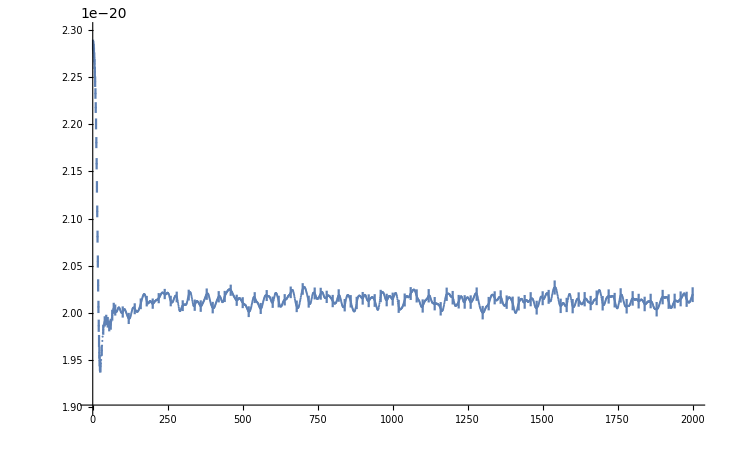

```mathematica
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True];
a=Table[{{1i,energycons[[1i]]},ErrorBar[error1[[1i]][[5]]]},{i,1,25}];
b=Table[{{5i,energycons[[5i]]},ErrorBar[error1[[5i]][[5]]]},{i,5,15}];
c=Table[{{20i,energycons[[20i]]},ErrorBar[error1[[20i]][[5]]]},{i,5,100}];
d=Join[a,b,c];
e=ListPlot[energycons,PlotRange->{{0,2000},{1.9*^-20,2.3*^-20}},PlotStyle->PointSize[0.002]];
f=ErrorListPlot[d,PlotRange->{{0,2000},{1.9*^-20,2.3*^-20}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

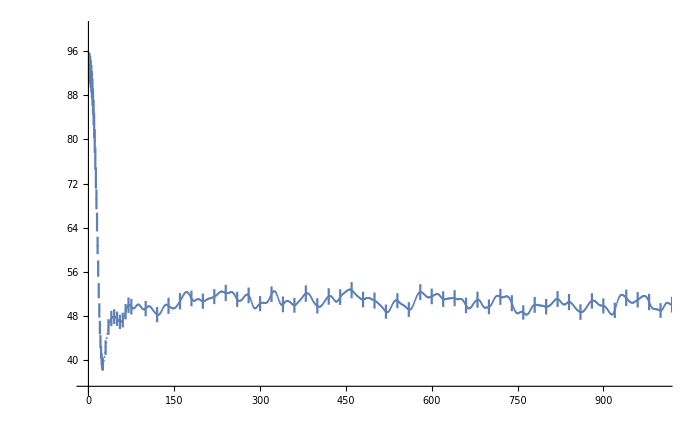

```mathematica
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True];
a=Table[{{1i,temperature[[1i]]},ErrorBar[error1[[1i]][[7]]]},{i,1,25}];
b=Table[{{5i,temperature[[5i]]},ErrorBar[error1[[5i]][[7]]]},{i,5,15}];
c=Table[{{20i,temperature[[20i]]},ErrorBar[error1[[20i]][[7]]]},{i,5,100}];
d=Join[a,b,c];
e=ListPlot[temperature,PlotRange->{{0,1000},{35,100}},PlotStyle->PointSize[0.002]];
f=ErrorListPlot[d,PlotRange->{{0,1000},{35,100}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

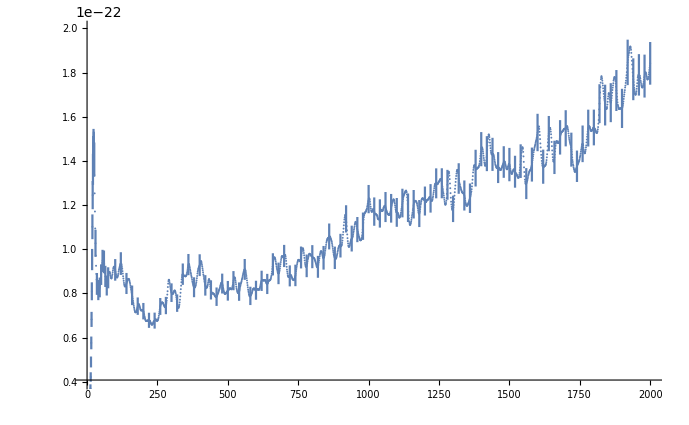

```mathematica
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True];
a=Table[{{1i,heatcap[[1i]]},ErrorBar[error1[[1i]][[8]]]},{i,1,25}];
b=Table[{{5i,heatcap[[5i]]},ErrorBar[error1[[5i]][[8]]]},{i,5,15}];
c=Table[{{20i,heatcap[[20i]]},ErrorBar[error1[[20i]][[8]]]},{i,5,100}];
d=Join[a,b,c];
e=ListPlot[heatcap,PlotRange->{{0,2000},{4*^-23,2*^-22}},PlotStyle->PointSize[0.002]];
f=ErrorListPlot[d,PlotRange->{{0,2000},{4*^-23,2*^-22}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

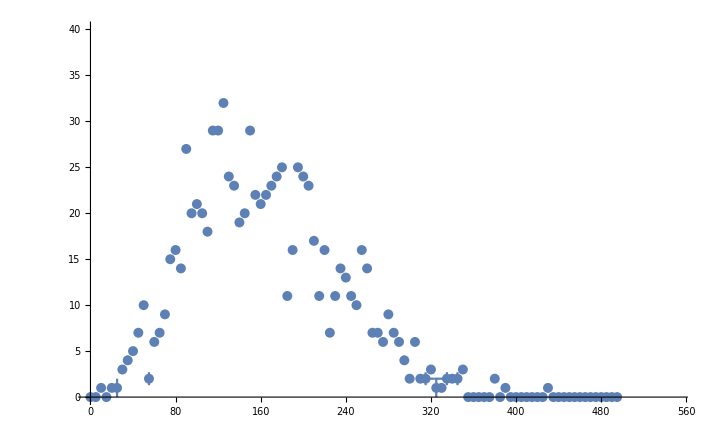

```mathematica
spderror = ReadList["~/phd-stuff/courses/astrid_sim/speederror.txt",Number,RecordLists->False];
spdbinerror = ReadList["~/phd-stuff/courses/astrid_sim/spdbinerror.txt",Number,RecordLists->False];
spdbinsize = ReadList["~/phd-stuff/courses/astrid_sim/spdbinsize.txt",Number,RecordLists->False];
a=Table[{{spdbinsize[[2i]],veldist[[2i]]},ErrorBar[spderror[[2i]],spdbinerror[[2i]]]},{i,50}];
b=Table[{5(i-1),veldist[[i]]},{i,1,100}];
e=ListPlot[b,PlotRange->{{0,550},{0,40}},PlotStyle->{PointSize[0.01]}];
f=ErrorListPlot[a,PlotRange->{{0,550},{0,40}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

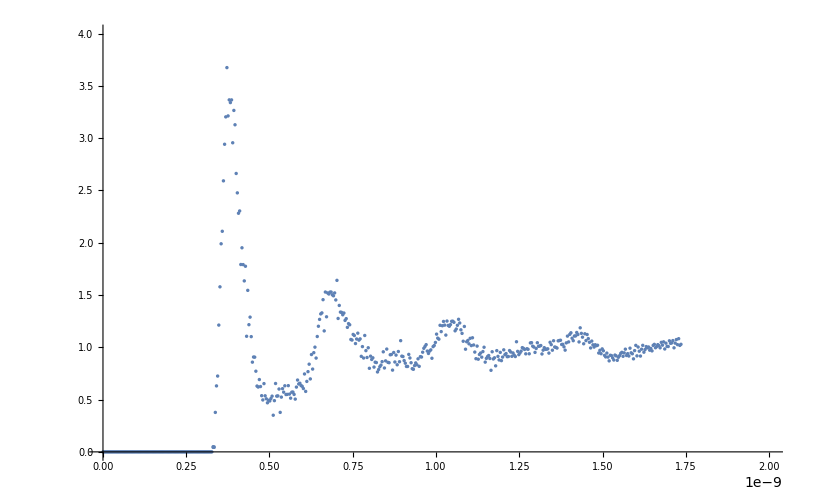

```mathematica
rdferror = ReadList["~/phd-stuff/courses/astrid_sim/rdferror.txt",Number,RecordLists->False];
rdfbinerror = ReadList["~/phd-stuff/courses/astrid_sim/rdfbinerror.txt",Number,RecordLists->False];
rdfbinsize = ReadList["~/phd-stuff/courses/astrid_sim/rdfbinsize.txt",Number,RecordLists->False];
a=Table[{{rdfbinsize[[i]],rdf[[i]]},ErrorBar[rdferror[[i]],rdfbinerror[[i]]]},{i,108}];
b=Table[{{rdfbinsize[[2i]],rdf[[2i]]},ErrorBar[rdferror[[2i]],rdfbinerror[[2i]]]},{i,54,75}];
bb=Table[{{rdfbinsize[[5i]],rdf[[5i]]},ErrorBar[rdferror[[5i]],rdfbinerror[[5i]]]},{i,30,100}];
c=Join[a,b,bb];
d=Table[{rdfbinsize[[i]],rdf[[i]]},{i,1,500}];
e=ListPlot[d,PlotRange->{{0,2*^-9},{0,4}},PlotStyle->{PointSize[0.003]}];
f=ErrorListPlot[c,PlotRange->{{0,2*^-9},{0,4}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

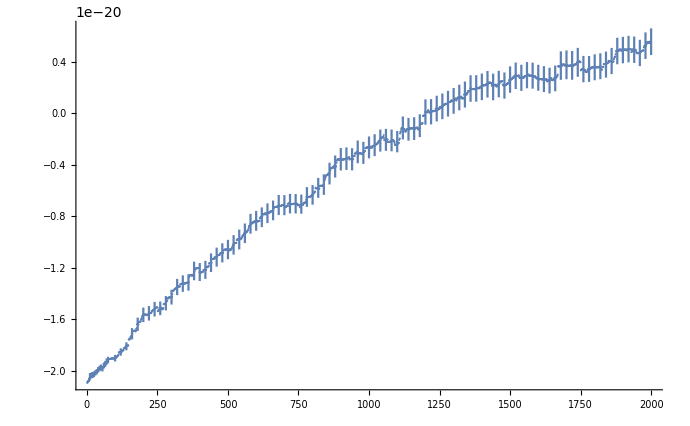

```mathematica
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True];
a=Table[{{1i,potential[[1i]]},ErrorBar[error1[[1i]][[3]]]},{i,1,25}];
b=Table[{{5i,potential[[5i]]},ErrorBar[error1[[5i]][[3]]]},{i,5,15}];
c=Table[{{20i,potential[[20i]]},ErrorBar[error1[[20i]][[3]]]},{i,5,100}];
d=Join[a,b,c];
e=ListPlot[potential,PlotRange->{{0,2000},{1.0*^-20,-2.15*^-20}},PlotStyle->PointSize[0.002]];
f=ErrorListPlot[d,PlotRange->{{0,2000},{1.0*^-20,-2.15*^-20}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

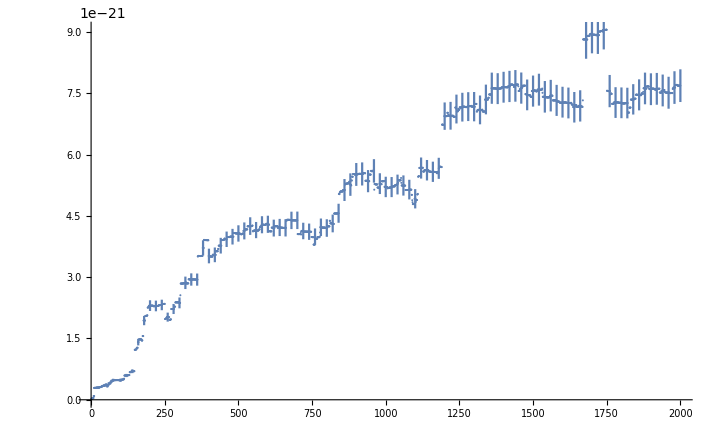

```mathematica
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True];
a=Table[{{1i,heatcap[[1i]]},ErrorBar[error1[[1i]][[8]]]},{i,1,25}];
b=Table[{{5i,heatcap[[5i]]},ErrorBar[error1[[5i]][[8]]]},{i,5,15}];
c=Table[{{20i,heatcap[[20i]]},ErrorBar[error1[[20i]][[8]]]},{i,5,100}];
d=Join[a,b,c];
e=ListPlot[heatcap,PlotRange->Automatic,PlotStyle->PointSize[0.002]];
f=ErrorListPlot[d,PlotRange->{{0,2000},{4*^-23,2*^-22}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

```mathematica
rdferror = ReadList["~/phd-stuff/courses/astrid_sim/rdferror.txt",Number,RecordLists->False];
rdfbinerror = ReadList["~/phd-stuff/courses/astrid_sim/rdfbinerror.txt",Number,RecordLists->False];
rdfbinsize = ReadList["~/phd-stuff/courses/astrid_sim/rdfbinsize.txt",Number,RecordLists->False];
a=Table[{{rdfbinsize[[i]],rdf[[i]]},ErrorBar[rdferror[[i]],rdfbinerror[[i]]]},{i,108}];
b=Table[{{rdfbinsize[[2i]],rdf[[2i]]},ErrorBar[rdferror[[2i]],rdfbinerror[[2i]]]},{i,54,75}];
bb=Table[{{rdfbinsize[[5i]],rdf[[5i]]},ErrorBar[rdferror[[5i]],rdfbinerror[[5i]]]},{i,30,100}];
c=Join[a,b,bb];
d=Table[{rdfbinsize[[i]],rdf[[i]]},{i,1,500}];
e=ListPlot[d,PlotRange->{{0,2*^-9},{0,4}},PlotStyle->{PointSize[0.003]}];
f=ErrorListPlot[c,PlotRange->{{0,2*^-9},{0,4}},PlotStyle->PointSize[0.0002]];
Show[e,f]
```

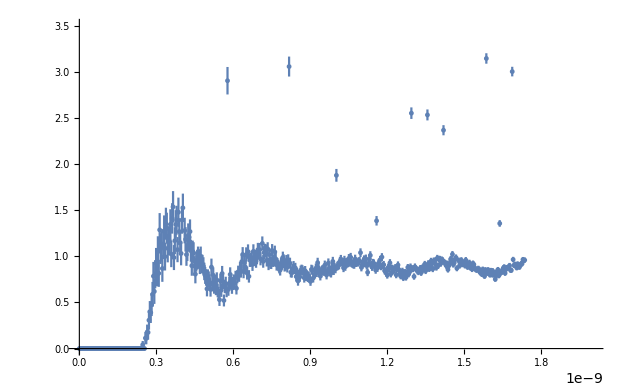

```mathematica
rdferror = ReadList["~/phd-stuff/courses/astrid_sim/rdferror.txt",Number,RecordLists->False];
rdfbinerror = ReadList["~/phd-stuff/courses/astrid_sim/rdfbinerror.txt",Number,RecordLists->False];
rdfbinsize = ReadList["~/phd-stuff/courses/astrid_sim/rdfbinsize.txt",Number,RecordLists->False];
error1 = ReadList["~/phd-stuff/courses/astrid_sim/error1.txt",Number,RecordLists->True]; 
ErrorListPlot[Table[{{i,heatcap[[i]]},ErrorBar[error1[[i]][[8]]]},{i,1,100}],PlotRange->All];
ErrorListPlot[Table[{{rdfbinsize[[i]],rdf[[i]]},ErrorBar[rdferror[[i]],rdfbinerror[[i]]]},{i,1,Length[rdferror]}],PlotRange->{{0,2*^-9},{0,3.5}}]
heatcap[[1]]
error1[[1]][[8]]
Length[heatcap]
```

{3026,5.68297×10^-26}

{3026,1.22536×10^-21}

{3029,1.22461×10^-21}

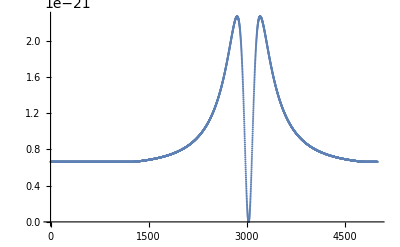

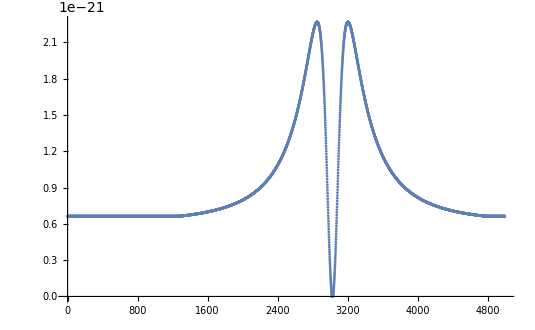

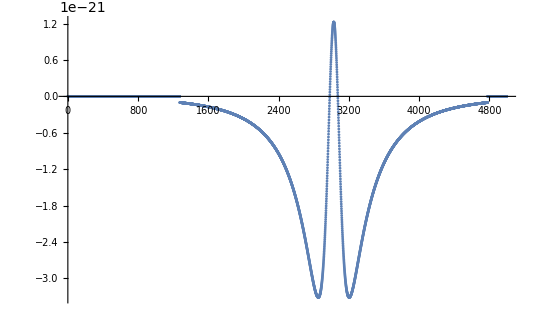

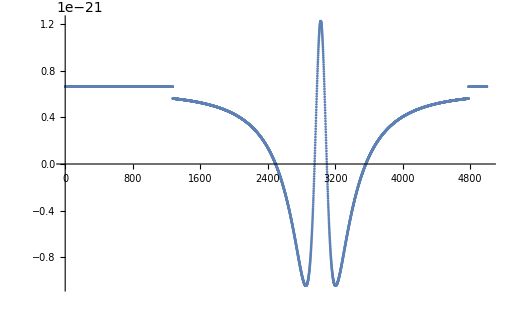

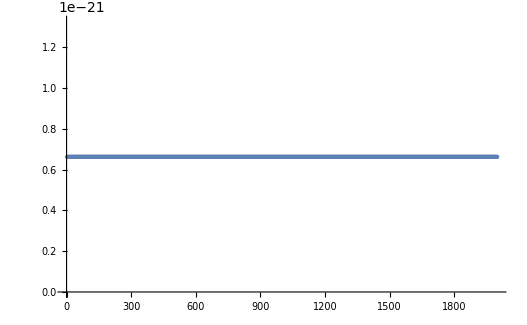

```mathematica
test = ReadList["~/phd-stuff/courses/astrid_sim/test.txt",Number,RecordLists->False];
kinenergytest=Table[test[[-2+3i]],{i,1,Length[test]/3-3}];
potenergytest=Table[test[[-1+3i]],{i,1,Length[test]/3-3}];
totenergytest=Table[test[[3i]],{i,1,Length[test]/3-3}];
kinenergytest2=Table[{i,test[[1+3i]]},{i,1,Length[test]/3-3}];
potenergytest2=Table[{i,test[[2+3i]]},{i,1,Length[test]/3-3}];
totenergytest2=Table[{i,test[[3i]]},{i,1,Length[test]/3}];

toten2 = Table[kinenergytest2[[i]]+potenergytest2[[i]],{i,1,1000}];

kinsorted=Sort[kinenergytest2,#1[[2]]<#2[[2]]&];
potsorted=Sort[potenergytest2,#1[[2]]<#2[[2]]&];
totsorted=Sort[totenergytest2,#1[[2]]<#2[[2]]&];

kinsorted[[1]]
potsorted[[Length[potsorted]]]
totsorted[[Length[potsorted]]]


ListPlot[kinenergytest]
ListPlot[Flatten@kinenergytest,PlotRange->All]
ListPlot[Flatten@potenergytest,PlotRange->All]
ListPlot[Flatten@totenergytest,PlotRange->All]

ListPlot[toten2]
```

```mathematica
initPositions
SortBy[initPositions,#[[3]]&];numvel=Table[{k,velocities[[k]]},{k,1,Length[velocities]}];
Sort[numvel,#1[[2]]>#2[[2]]&];
```

```mathematica
initPositions[[1]]
initPositions[[2]]
initPositions[[3]]
initPositions[[4]]
initPositions[[5]]
initPositions[[6]]
```

{2.47836×10^-9,2.47836×10^-9,2.47836×10^-9}

{10,10,10}

{9.95028×10^-24,-3.81431×10^-25}

{3.47736×10^-9,3.47736×10^-9,3.47736×10^-9}

{-10,-10,-10}

{9.95028×10^-24,-3.81431×10^-25}

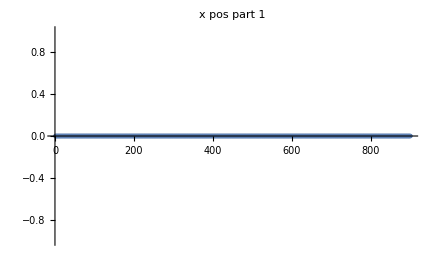

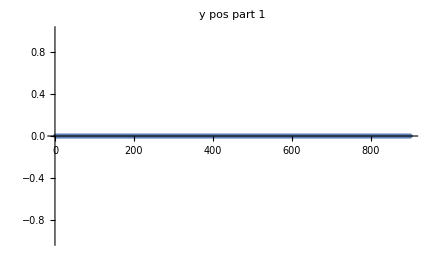

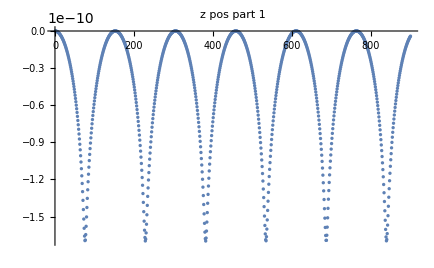

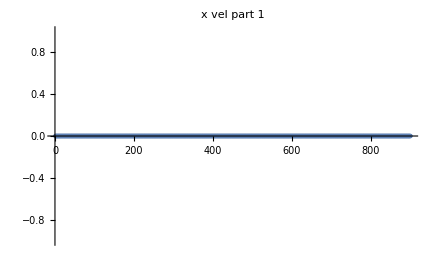

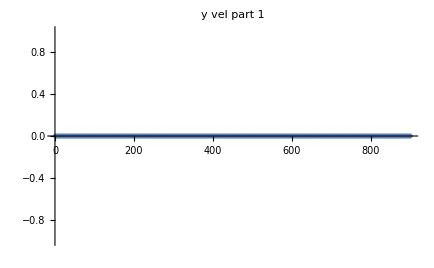

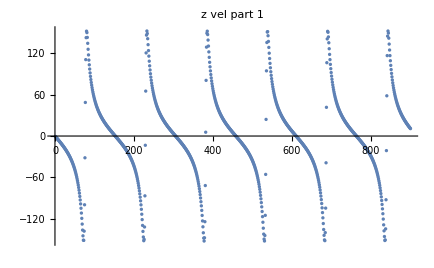

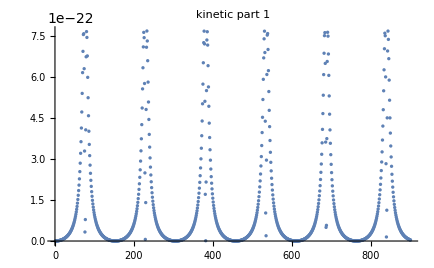

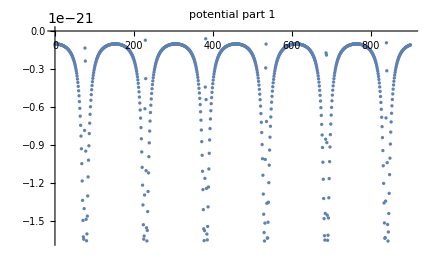

```mathematica
scaleFactor=10^0;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/testpositions.txt",Number,RecordLists->True]*scaleFactor;
pos11=Table[initPositions[[1+6i]][[1]],{i,0,900}];
pos12=Table[initPositions[[1+6i]][[2]],{i,0,900}];
pos13=Table[initPositions[[1+6i]][[3]],{i,0,900}];
vel11=Table[initPositions[[2+6i]][[1]]  ,{i,0,900}];
vel12=Table[initPositions[[2+6i]][[2]]  ,{i,0,900}];
vel13=Table[initPositions[[2+6i]][[3]]  ,{i,0,900}];
kin1 = Table[initPositions[[3+6i]][[1]],{i,0,900}];
pot1= Table[initPositions[[3+6i]][[2]],{i,0,900}];
pos21=Table[initPositions[[4+6i]][[1]],{i,0,900}];
vel21=Table[initPositions[[5+6i]][[1]],{i,0,900}];
kin2 = Table[initPositions[[0+6i]][[1]],{i,1,900}];
pot2= Table[initPositions[[0+6i]][[2]],{i,1,900}];

ListPlot[pos11,PlotLabel->"x pos part 1"]
ListPlot[pos12,PlotLabel->"y pos part 1"]
ListPlot[pos13,PlotLabel->"z pos part 1"]
ListPlot[vel11,PlotLabel->"x vel part 1"]
ListPlot[vel12,PlotLabel->"y vel part 1"]
ListPlot[vel13,PlotLabel->"z vel part 1"]
ListPlot[kin1,PlotLabel->"kinetic part 1"]
ListPlot[pot1,PlotLabel->"potential part 1"]
ListPlot[kin1+pot1,PlotLabel->"energy conservation"]
```

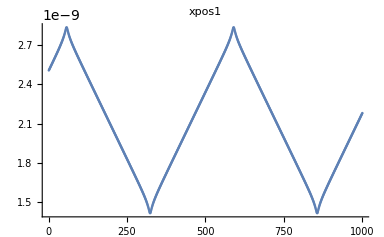

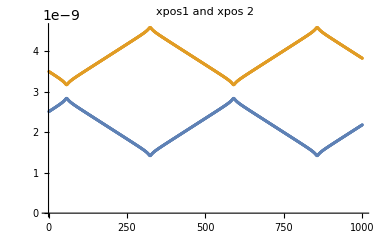

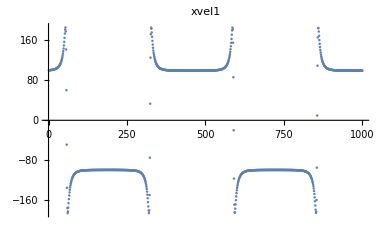

-Graphics-

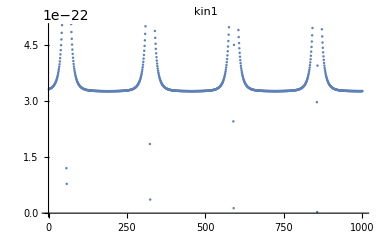

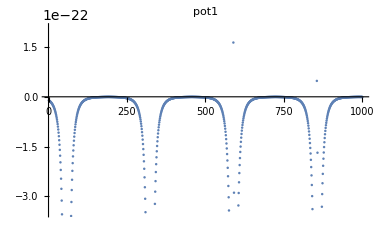

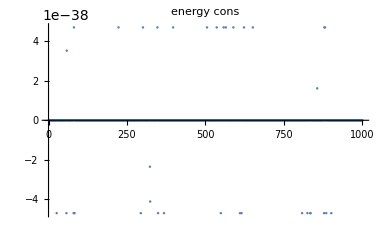

```mathematica
verlet= ReadList["~/phd-stuff/courses/astrid_sim/periodicverlet.txt",Number,RecordLists->True];

xpos=Table[verlet[[1+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];
v=Table[verlet[[1+4*i]][[2]],{i,0,Length[(verlet)]/4-1}];
kin=Table[verlet[[1+4*i]][[3]],{i,0,Length[(verlet)]/4-1}];
pot=Table[verlet[[1+4*i]][[4]],{i,0,Length[(verlet)]/4-1}];
acc=Table[verlet[[4+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];

xpos2=Table[verlet[[2+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];
v2=Table[verlet[[2+4*i]][[2]],{i,0,Length[(verlet)]/4-1}];
kin2=Table[verlet[[2+4*i]][[3]],{i,0,Length[(verlet)]/4-1}];
pot2=Table[verlet[[2+4*i]][[4]],{i,0,Length[(verlet)]/4-1}];

ListPlot[{xpos},PlotLabel->"xpos1"]
ListPlot[{xpos2},PlotLabel->"xpos2"];

ListPlot[{xpos,xpos2},PlotLabel->"xpos1 and xpos 2"]

ListPlot[{v},PlotLabel->"xvel1"]
ListPlot[{v2},PlotLabel->"xvel2"];

ListPlot[{acc},PlotLabel->"acc1"]

ListPlot[{kin},PlotLabel->"kin1"]
ListPlot[{kin2},PlotLabel->"kin2"];

ListPlot[{pot},PlotLabel->"pot1"]
ListPlot[{pot2},PlotLabel->"pot2"];

ListPlot[{kin+pot-(kin2+pot2)},PlotLabel->"energy cons"]
```

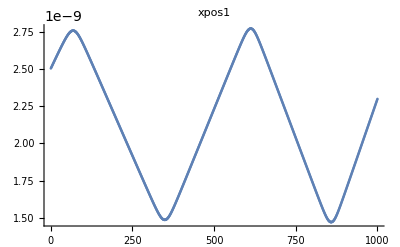

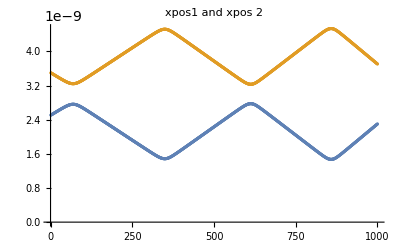

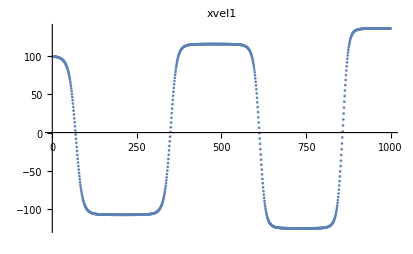

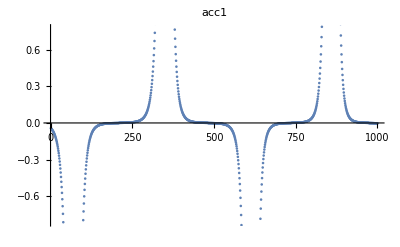

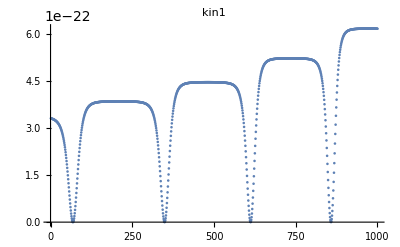

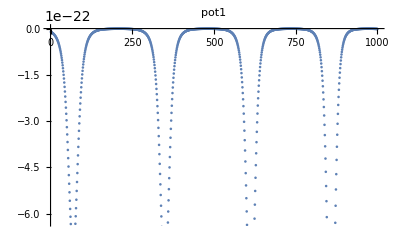

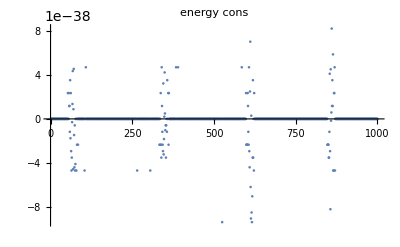

```mathematica
verlet= ReadList["~/phd-stuff/courses/astrid_sim/periodicrk.txt",Number,RecordLists->True];

xpos=Table[verlet[[1+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];
v=Table[verlet[[1+4*i]][[2]],{i,0,Length[(verlet)]/4-1}];
kin=Table[verlet[[1+4*i]][[3]],{i,0,Length[(verlet)]/4-1}];
pot=Table[verlet[[1+4*i]][[4]],{i,0,Length[(verlet)]/4-1}];
acc=Table[verlet[[4+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];

xpos2=Table[verlet[[2+4*i]][[1]],{i,0,Length[(verlet)]/4-1}];
v2=Table[verlet[[2+4*i]][[2]],{i,0,Length[(verlet)]/4-1}];
kin2=Table[verlet[[2+4*i]][[3]],{i,0,Length[(verlet)]/4-1}];
pot2=Table[verlet[[2+4*i]][[4]],{i,0,Length[(verlet)]/4-1}];

ListPlot[{xpos},PlotLabel->"xpos1"]
ListPlot[{xpos2},PlotLabel->"xpos2"];

ListPlot[{xpos,xpos2},PlotLabel->"xpos1 and xpos 2"]

ListPlot[{v},PlotLabel->"xvel1"]
ListPlot[{v2},PlotLabel->"xvel2"];

ListPlot[{acc},PlotLabel->"acc1"]

ListPlot[{kin},PlotLabel->"kin1"]
ListPlot[{kin2},PlotLabel->"kin2"];

ListPlot[{pot},PlotLabel->"pot1"]
ListPlot[{pot2},PlotLabel->"pot2"];

ListPlot[{kin+pot-(kin2+pot2)},PlotLabel->"energy cons"]
```

4 ϵ (-σ^6/r^6+σ^12/r^12)

-4 ϵ ((6 σ^6)/r^7-(12 σ^12)/r^13)

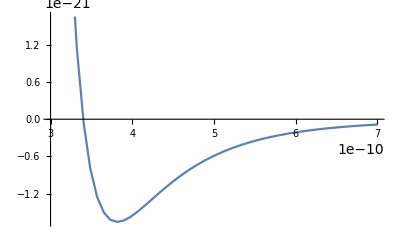

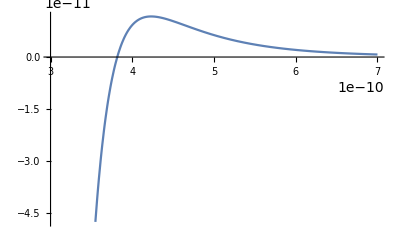

```mathematica
T=120;
sigma=3.4*^-10;
kB=1.38064852*^-23;
epsilon=T*kB;
umass=1.660539040*^-27;
argonmass=umass*39.948;

min = 3*^-10;
max = 7*^-10;

4*ϵ*((σ/r)^12-(σ/r)^6)
-D[%,r]

Plot[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Plot[4 epsilon ((6 sigma^6)/r^7-(12 sigma^12)/r^13),{r,min,max}]

Manipulate[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Manipulate[4 epsilon (-(6 sigma^6)/r^7+(12 sigma^12)/r^13),{r,min,max}]
```

```mathematica
Sqrt[1.156*^-19]
-1.1694905110588235*^-10*2
```

3.4×10^-10

-2.33898×10^-10

```mathematica
scaleFactor=10^9;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/radialdistpos.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

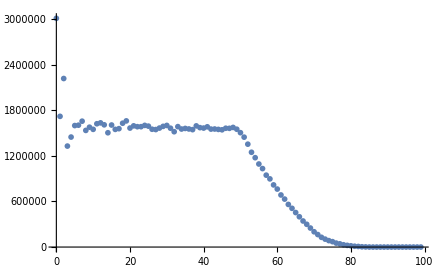

```mathematica
rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->True];
ListPlot[rdf]
```

```mathematica
sigma=3.4*^-10;
boxlength=10.229*sigma;
```

3.47786×10^-9

6.95572×10^-10

3.01192×10^-9

3.01192×10^-9